```mathematica
$Assumptions = {k1 ∈ Reals, k2 ∈Reals, t ∈ Reals, s ∈ Reals, m ∈ Reals}
```

{k1∈ℝ,k2∈ℝ,t∈ℝ,s∈ℝ,m∈ℝ}

```mathematica
L ={{-(k1+k2), (k2+k1)},{(k2+k1), -(k1+k2)}}
```

{{-k1-k2,k1+k2},{k1+k2,-k1-k2}}

```mathematica
Eigenvectors[L]
```

{{-1,1},{1,1}}

```mathematica
Eigenvalues[L]
```

{-2 (k1+k2),0}

```mathematica
S = {{0,t + s Exp[ⅈ k]},{t + s Exp[-ⅈ k],0}}
```

{{0,ⅇ^(ⅈ k) s+t},{ⅇ^(-ⅈ k) s+t,0}}

```mathematica
ev = Eigenvalues[S]//FullSimplify
```

{-ⅇ^(-ⅈ k) √(ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k])),ⅇ^(-ⅈ k) √(ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k]))}

```mathematica
ev[[2]]/.s->1/.t->0.5/.k->0
```

1.5

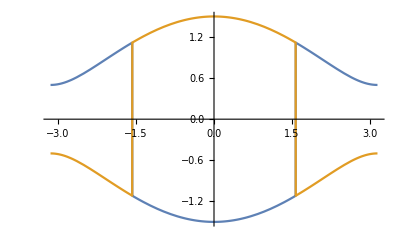

```mathematica
Plot[{ev[[1]]/.s->1/.t->0.5,ev[[2]]/.s->1/.t->0.5}, {k, -π, π}]
```

Try with |m> = cos(t) + sin(t)

```mathematica
ClearAll["Global`*"]
```

```mathematica
mket  = Cos[k m] + Sin[k m]
```

Cos[k m]+Sin[k m]

```mathematica
mkete = TrigToExp[mket]
```

(1/2+ⅈ/2) ⅇ^(-ⅈ k m)+(1/2-ⅈ/2) ⅇ^(ⅈ k m)

```mathematica
mkete Conjugate[mkete]//ComplexExpand//FullSimplify
```

1+Sin[2 k m]

```mathematica
m1ket = Cos[k (m+1)] + Sin[k (m+1)]
```

Cos[k (1+m)]+Sin[k (1+m)]

```mathematica
m1kete = TrigToExp[m1ket]
```

(1/2+ⅈ/2) ⅇ^(-ⅈ k (1+m))+(1/2-ⅈ/2) ⅇ^(ⅈ k (1+m))

```mathematica
m1kete Conjugate[mkete]//ComplexExpand//FullSimplify
```

Cos[k]+Sin[k+2 k m]

```mathematica
1/2 (PauliMatrix[1] + ⅈ PauliMatrix[2])//FullSimplify//MatrixForm
```

(0 | 1
0 | 0)

```mathematica
1/2 (PauliMatrix[1] - ⅈ PauliMatrix[2])//FullSimplify//MatrixForm
```

(0 | 0
1 | 0)